```mathematica
(* Compute the line integral
∫_C (x y^2 ⅆy - x^2 y ⅆx) , where C is the cardioid r = (1+Cos[θ]) 
https://www.quora.com/How-do-you-evaluate-the-line-integral-int_C-xy-2-dy-x-2y-dx-where-C-is-the-cardioid-r-a-1-cos-theta
*)
```

```mathematica
(* Cardioid: *)
c[θ_]:= a(1+Cos[θ])
```

```mathematica
(* Use Green's theorem: ∫_C v[x,y]∫∫_R curl v[x,y] *)
(* 1) Vector field: *)v[x_,y_]:={-x^2 y ,x y^2}
```

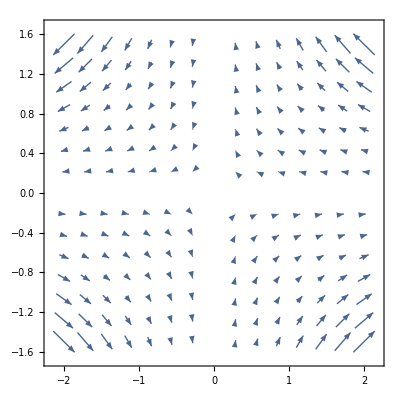

```mathematica
(* Visualize the vector field (and cardioid) for the line integral: *)
VectorPlot[v[x,y],{x,-2,2},{y,-1.5,1.5},PlotRangePadding->None]
```

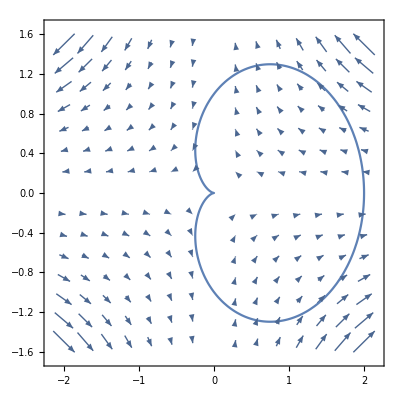

```mathematica
Show[%, PolarPlot[c[θ]/.a-> 1, {θ, 0, 2π}]]
```

```mathematica
(* The circulation of the vector field can be computed using Curlpaclet:ref/Curl: *)
circ = Curl[v[x,y],{x,y}]
```

x^2+y^2

```mathematica
(* Now, integrate over the interior of the Cardioid: *)
(* 1) Convert to Polar Coordinates: *)
circPolar= TransformedField["Cartesian"-> "Polar",circ,{x, y}-> {r, θ}]//FullSimplify
```

r^2

```mathematica
(* 2) Area element: Use Jacobian determinant of the coordinate conversion formula *)
(* (Inverse) coordinate conversion formula: *) transf = FromPolarCoordinates[{r, θ}]
```

{r Cos[θ],r Sin[θ]}

```mathematica
(* Jacobian matrix: *)
J= Grad[transf, {r, θ}]
```

{{Cos[θ],-r Sin[θ]},{Sin[θ],r Cos[θ]}}

```mathematica
(* Jacobian matrix determinant: *)
detJ = Det[J]//FullSimplify
```

r

```mathematica
∫_0^(2π) ∫_0^(r/.r-> a(1+Cos[θ])) circPolar detJ ⅆrⅆθ
```

(35 a^4 π)/16

```mathematica
(* That's it! *)
```

```mathematica
(* Another example of Jacobian determinant (spherical coordinates): *)
```

```mathematica
transf = FromSphericalCoordinates[{r, θ, ϕ}]
```

{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ]}

```mathematica
(* Jacobian matrix: *)
J= Grad[transf, {r, θ, ϕ}];
J//MatrixForm
```

(Cos[ϕ] Sin[θ] | r Cos[θ] Cos[ϕ] | -r Sin[θ] Sin[ϕ]
Sin[θ] Sin[ϕ] | r Cos[θ] Sin[ϕ] | r Cos[ϕ] Sin[θ]
Cos[θ] | -r Sin[θ] | 0)

```mathematica
(* Jacobian matrix determinant: *)
detJ = Det[J]//FullSimplify
```

r^2 Sin[θ]

```mathematica
(* :-) *)
```

```mathematica
(* Another, from polar to cartesian: *)
```

```mathematica
transf = ToPolarCoordinates[{x,y}]
```

{√(x^2+y^2),ArcTan[x,y]}

```mathematica
(* Jacobian matrix: *)
J= Grad[transf, {x, y}];
J//MatrixForm
```

(x/(√(x^2+y^2)) | y/(√(x^2+y^2))
-y/(x^2+y^2) | x/(x^2+y^2))

```mathematica
(* Jacobian matrix determinant: *)
detJ = Det[J]//FullSimplify
```

1/(√(x^2+y^2))

```mathematica
(* Another, from spherical to cartesian: *)
```

```mathematica
transf = ToSphericalCoordinates[{x,y, z}]
```

{√(x^2+y^2+z^2),ArcTan[z,√(x^2+y^2)],ArcTan[x,y]}

```mathematica
(* Jacobian matrix: *)
J= Grad[transf, {x, y,z}];
J//MatrixForm
```

(x/(√(x^2+y^2+z^2)) | y/(√(x^2+y^2+z^2)) | z/(√(x^2+y^2+z^2))
(x z)/(√(x^2+y^2) (x^2+y^2+z^2)) | (y z)/(√(x^2+y^2) (x^2+y^2+z^2)) | -(√(x^2+y^2))/(x^2+y^2+z^2)
-y/(x^2+y^2) | x/(x^2+y^2) | 0)

```mathematica
(* Jacobian matrix determinant: *)
detJ = Det[J]//FullSimplify
```

1/(√(x^2+y^2) √(x^2+y^2+z^2))